```mathematica
"1.3212142437597074`,0.6175674663771106`,1.5850439018133249`";
V1=-6;mu=-0.32;
ClearAll[f]
f[k_,eps0_,eps1_,eps2_,Δ1_,Δ2_]:=With[{ω=Exp[(2 π I)/3],t1=2^(1/3),t2=2^(2/3)},Module[{A,B,disc,c},(*A is the combination that appears repeatedly in Cardano’s formula*)A=9 Δ1^2 eps0+9 Δ2^2 eps0+2 eps0^3-9 Δ1^2 eps1+18 Δ2^2 eps1+3 eps0^2 eps1-3 eps0 eps1^2-2 eps1^3+18 Δ1^2 eps2-9 Δ2^2 eps2+3 eps0^2 eps2+12 eps0 eps1 eps2+3 eps1^2 eps2-3 eps0 eps2^2+3 eps1 eps2^2-2 eps2^3;
(*B is defined as in the simplified Cardano expression*)B=-(eps0-eps1-eps2)^2-3 (Δ1^2+Δ2^2+eps0 eps1+eps0 eps2-eps1 eps2);
disc=Sqrt[A^2+4 B^3];
(*Compute the cube-root once*)c=(A+disc)^(1/3);
(*Return the kth solution (k=0,1,or 2)*)(eps0-eps1-eps2)/3+(ω^k*c-ω^(-k)*t2*B/c)/(3*t1)]]
(*define some structure*)
Factor1[E1_,E2_,E3_,eps1_,eps2_]:=Module[{},
(E1+eps1)(E1+eps2)/(E1-E2)/(E1-E3)
]

Factor2[E1_,E2_,E3_,eps1_,Delta_]:=Module[{},
Delta*(E1+eps1)/(E1-E2)/(E1-E3)
]
(**)
t=1;t'=0.3t;
Qy=0;  
Dispersion[x_,y_]:=-2t(Cos[x]+Cos[y])+4t'Cos[x]*Cos[y]-mu;

Shaped[x_,y_]:=Cos[x]-Cos[y];
Shapes[x_,y_]:=Cos[x]+Cos[y];

fepsi[x_,y_]:=Dispersion[x,y];
fepsi1[x_,y_,Qx_]:=Dispersion[x-Qx,y-Qy];
fepsi2[x_,y_,Qx_]:=Dispersion[x+Qx,y+Qy];

Band1[x_,y_,Qx_,Des_,Ded_]:=f[1,fepsi[x,y],fepsi1[x,y,Qx],fepsi2[x,y,Qx],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band2[x_,y_,Qx_,Des_,Ded_]:=f[2,fepsi[x,y],fepsi1[x,y,Qx],fepsi2[x,y,Qx],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];
Band3[x_,y_,Qx_,Des_,Ded_]:=f[3,fepsi[x,y],fepsi1[x,y,Qx],fepsi2[x,y,Qx],Des*Shapes[x-Qx/2,y]+Ded*Shaped[x-Qx/2,y],Des*Shapes[x+Qx/2,y]+Ded*Shaped[x+Qx/2,y]];

Thermal[E_,T_]:=1/(  Exp[E/T] +1   );

Factor2[E1_,E2_,E3_,eps1_,Delta_]:=Module[{},
Delta*(E1+eps1)/(E1-E2)/(E1-E3)
]

DIntSolveGap[Qx_,Des_,Ded_,px_,py_]:=Module[{ Result,fact,T,cy1,cy2,Kinetic,Potential,Nshape1,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
E1n=Band1[px,py,Qx,Des,Ded];E2n=Band2[px,py,Qx,Des,Ded];E3n=Band3[px,py,Qx,Des,Ded];
eps1n=fepsi1[px,py,Qx];
(**)
T=0.005;
Ffact=Des*Shapes[px+Qx/2,py]+Ded*Shaped[px+Qx/2,py];
Symfact=Shaped[px+Qx/2,py];
Nresult1=Thermal[E1n,T]*Factor2[E1n,E2n,E3n,eps1n,Ffact]*Symfact;
Nresult2=Thermal[E2n,T]*Factor2[E2n,E1n,E3n,eps1n,Ffact]*Symfact;
Nresult3=Thermal[E3n,T]*Factor2[E3n,E1n,E2n,eps1n,Ffact]*Symfact;
 
(*For definiteness let us consider y-direction response*)
Result=V1*(Nresult1 +Nresult2 +Nresult3 );
(Re[Result]/Ded )/(2*Pi)^2
]

SIntSolveGap[Qx_,Des_,Ded_,px_,py_]:=Module[{ Result,fact,T,cy1,cy2,Kinetic,Potential,Nshape1,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
E1n=Band1[px,py,Qx,Des,Ded];E2n=Band2[px,py,Qx,Des,Ded];E3n=Band3[px,py,Qx,Des,Ded];
eps1n=fepsi1[px,py,Qx];
(**)
T=0.005;
Ffact=Des*Shapes[px+Qx/2,py]+Ded*Shaped[px+Qx/2,py];
Symfact=Shapes[px+Qx/2,py];
Nresult1=Thermal[E1n,T]*Factor2[E1n,E2n,E3n,eps1n,Ffact]*Symfact;
Nresult2=Thermal[E2n,T]*Factor2[E2n,E1n,E3n,eps1n,Ffact]*Symfact;
Nresult3=Thermal[E3n,T]*Factor2[E3n,E1n,E2n,eps1n,Ffact]*Symfact;
(*For definiteness let us consider y-direction response*)
Result=V1*(Nresult1 +Nresult2 +Nresult3 );
(Re[Result]/Des )/(2*Pi)^2
]



(*Domain limits for px and py*)
pxMin=-Pi;
pxMax=Pi;
pyMin=-Pi;
pyMax=Pi;
 
SSolveGap[Qx_,Des_,Ded_]:=NIntegrate[SIntSolveGap[Qx,Des,Ded,px,py],{px,pxMin,pxMin/2,pxMax/2,pxMax},{py,pxMin,pxMin/2,pxMax/2,pxMax}, Method->{"LocalAdaptive"}]; 

DSolveGap[Qx_,Des_,Ded_]:=NIntegrate[DIntSolveGap[Qx,Des,Ded,px,py],{px,pxMin,pxMin/2,pxMax/2,pxMax},{py,pxMin,pxMin/2,pxMax/2,pxMax}, Method->{"LocalAdaptive"}];
```

```mathematica
s0=0.58;
d0=1.54; 
SSolveGap[0.39*Pi,s0,d0]
DSolveGap[0.39*Pi,s0,d0]
{0.39*Pi,s0,d0}
```

1.00246

1.00424

{1.22522,0.58,1.54}

```mathematica
s0=0.65;
d0=1.55;  
SSolveGap[0.5*Pi,s0,d0]
DSolveGap[0.5*Pi,s0,d0]
{0.5*Pi,s0,d0}
```

0.99554

1.01408

{1.5708,0.65,1.55}

```mathematica
{QMin,QMax,QStep}={1.2828170002158321,1.340412865531645,(1.340412865531645-1.2828170002158321)/6};

(*1) Your raw data:{x,y2,y3}*)data={{1.2828170002158321,0.5907191908314691,1.5556891174918985},{1.340412865531645,0.5987876231266922,1.5634752517015016}};

(*2) Fit y2=f2(x) and y3=f3(x)*)
f2[x_]=Fit[data[[All,{1,2}]],{1,x},x];
f3[x_]=Fit[data[[All,{1,3}]],{1,x},x];

(*4) Build a table of {x,f2(x),f3(x)} at equal intervals*)
userdata=Table[{q,f2[q],f3[q]},{q,QMin,QMax,QStep}]
```

{{1.28282,0.590719,1.55569},{1.29242,0.592064,1.55699},{1.30202,0.593409,1.55828},{1.31161,0.594753,1.55958},{1.32121,0.596098,1.56088},{1.33081,0.597443,1.56218},{1.34041,0.598788,1.56348}}

```mathematica
(*===1) Compile your SSolveGap& DSolveGap with p as a first argument===*)
cfSSg=Compile[{{p,_Real},{s,_Real},{d,_Real}},SSolveGap[p,s,d],CompilationOptions->{"InlineExternalDefinitions"->True}];
cfDSg=Compile[{{p,_Real},{s,_Real},{d,_Real}},DSolveGap[p,s,d],CompilationOptions->{"InlineExternalDefinitions"->True}];

(*===2) Numeric-only wrappers that subtract 1===*)
fSSg[p_?NumericQ,s_?NumericQ,d_?NumericQ]:=cfSSg[p,s,d]-1;
fDSg[p_?NumericQ,s_?NumericQ,d_?NumericQ]:=cfDSg[p,s,d]-1;

(*===3) Run FindRoot for each triple in userdata===*)
solutions=userdata/. {p_,s0_,d0_}:>Module[{s,d},FindRoot[{fSSg[p,s,d],fDSg[p,s,d]},{s,s0},{d,d0},Method->"Newton",AccuracyGoal->4,PrecisionGoal->4]];

pList=userdata[[All,1]];

(*2) turn each rule-pair into a {s,d} list*)
sdPairs=solutions[[All,All,2]];
(*{{s1,d1},{s2,d2},…}*)

(*3a) prepend each {s,d} with its p*)
updatedData=MapThread[Prepend,{sdPairs,pList}];

(* *or*equivalently**)

(*3b) build by transposition*)
updatedData=Transpose[{pList,sdPairs[[All,1]],sdPairs[[All,2]]}]
```

{{1.28282,0.61245,1.57956},{1.29242,0.613689,1.58097},{1.30202,0.615003,1.58232},{1.31161,0.616303,1.5837},{1.32121,0.617567,1.58504},{1.33081,0.618784,1.58637},{1.34041,0.620072,1.58757}}

```mathematica
(*now updatedData is {{p1,s1,d1},{p2,s2,d2},…}*)
```

```mathematica
results=Map[{SSolveGap[#[[1]],#[[2]],#[[3]]],DSolveGap[#[[1]],#[[2]],#[[3]]]}&,updatedData];
results
```

{{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.},{1.,1.}}

{{1.28282,0.61245,1.57956,-0.390281-4.25294×10^-17 ⅈ},{1.29242,0.613689,1.58097,-0.389303-3.44515×10^-17 ⅈ},{1.30202,0.615003,1.58232,-0.388332-4.61749×10^-17 ⅈ},{1.31161,0.616303,1.5837,-0.387359-2.67612×10^-17 ⅈ},{1.32121,0.617567,1.58504,-0.386401-2.98368×10^-17 ⅈ},{1.33081,0.618784,1.58637,-0.385443-2.85903×10^-17 ⅈ},{1.34041,0.620072,1.58757,-0.3845-4.79511×10^-17 ⅈ}}

{{1.28282,0.61245,1.57956,-0.478354-6.52642×10^-18 ⅈ},{1.29242,0.613689,1.58097,-0.479347-9.96202×10^-18 ⅈ},{1.30202,0.615003,1.58232,-0.480333-5.75517×10^-18 ⅈ},{1.31161,0.616303,1.5837,-0.481323-1.08246×10^-18 ⅈ},{1.32121,0.617567,1.58504,-0.482285-3.25385×10^-18 ⅈ},{1.33081,0.618784,1.58637,-0.483242+3.2916×10^-18 ⅈ},{1.34041,0.620072,1.58757,-0.484183-8.74803×10^-18 ⅈ}}

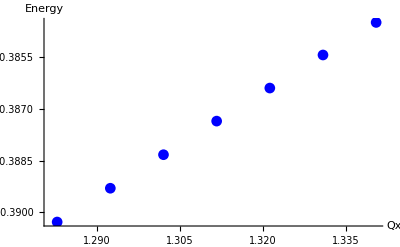

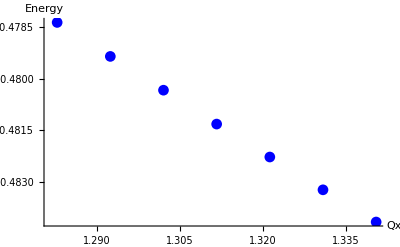

```mathematica
XYZData=updatedData;Kinet[Qx_,Des_,Ded_,px_,py_]:=Module[{ Fluct,AFluct,epsi,T,cy1,cy2,Kinetic,Potential,Nshape1,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
E1n=Band1[px,py,Qx,Des,Ded];E2n=Band2[px,py,Qx,Des,Ded];E3n=Band3[px,py,Qx,Des,Ded];

eps1n=fepsi1[px,py,Qx];eps2n=fepsi2[px,py,Qx];
(**)
T=0.005;
epsi=fepsi[px,py];
(*Kinetic*)
Nresult1=Thermal[E1n,T]*Factor1[E1n,E2n,E3n,eps1n,eps2n];
Nresult2=Thermal[E2n,T]*Factor1[E2n,E1n,E3n,eps1n,eps2n];
Nresult3=Thermal[E3n,T]*Factor1[E3n,E1n,E2n,eps1n,eps2n];
Kinetic=(Nresult1 +Nresult2 +Nresult3 )*epsi;
(Kinetic)/(2*Pi)^2     (*((Kinetic+Fluct+AFluct)-Potential )/(2*Pi)^2 *)
]

Potent[Qx_,Des_,Ded_,px_,py_]:=Module[{ Fluct,AFluct,epsi,T,cy1,cy2,Kinetic,Potential,Nshape1,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
E1n=Band1[px,py,Qx,Des,Ded];E2n=Band2[px,py,Qx,Des,Ded];E3n=Band3[px,py,Qx,Des,Ded];

eps1n=fepsi1[px,py,Qx];eps2n=fepsi2[px,py,Qx];
(**)
T=0.005;
epsi=fepsi[px,py];
(*Kinetic*)
Ffact=Des*Shapes[px+Qx/2,py]+Ded*Shaped[px+Qx/2,py];
Oresult1=Thermal[E1n,T]*Factor2[E1n,E2n,E3n,eps1n,Ffact]*Ffact;
Oresult2=Thermal[E2n,T]*Factor2[E2n,E1n,E3n,eps1n,Ffact]*Ffact;
Oresult3=Thermal[E3n,T]*Factor2[E3n,E1n,E2n,eps1n,Ffact]*Ffact;
Potential=(Oresult1 +Oresult2 +Oresult3 );
Potential/(2*Pi)^2     (*((Kinetic+Fluct+AFluct)-Potential )/(2*Pi)^2 *)
]

Potent1[Qx_,Des_,Ded_,px_,py_]:=Module[{ Fluct,AFluct,epsi,T,cy1,cy2,Kinetic,Potential,Nshape1,Nshape,order,fre,kx,ky,pxp,pxn,pyp,pyn,E1p,E2p,E3p,E1n,E2n,E3n,eps1p,eps2p,eps1n,eps2n},
E1n=Band1[px,py,Qx,Des,Ded];E2n=Band2[px,py,Qx,Des,Ded];E3n=Band3[px,py,Qx,Des,Ded];

eps1n=fepsi1[px,py,Qx];eps2n=fepsi2[px,py,Qx];
(**)
T=0.005;
epsi=fepsi[px,py];
(*Kinetic*)
Ffact=Des*Shapes[px-Qx/2,py]+Ded*Shaped[px-Qx/2,py];
Oresult1=Thermal[E1n,T]*Factor2[E1n,E2n,E3n,eps2n,Ffact]*Ffact;
Oresult2=Thermal[E2n,T]*Factor2[E2n,E1n,E3n,eps2n,Ffact]*Ffact;
Oresult3=Thermal[E3n,T]*Factor2[E3n,E1n,E2n,eps2n,Ffact]*Ffact;
Potential=(Oresult1 +Oresult2 +Oresult3 );
Potential/(2*Pi)^2     (*((Kinetic+Fluct+AFluct)-Potential )/(2*Pi)^2 *)
]


 


(*Domain limits for px and py*)
pxMin=-Pi;
pxMax=Pi;
pyMin=-Pi;
pyMax=Pi;

IntKineticIntegrated[Qx_,Des_,Ded_]:=NIntegrate[Kinet[Qx,Des,Ded,px,py],{px,pxMin,pxMin/2,pxMax/2,pxMax},{py,pxMin,pxMin/2,pxMax/2,pxMax}, Method->{"LocalAdaptive"}];

IntPotentialIntegrated[Qx_,Des_,Ded_]:=NIntegrate[Potent1[Qx,Des,Ded,px,py],{px,pxMin,pxMin/2,pxMax/2,pxMax},{py,pxMin,pxMin/2,pxMax/2,pxMax}, Method->{"LocalAdaptive"}];
 
evaluatedKArray=Map[{#[[1]],#[[2]],#[[3]],IntKineticIntegrated[#[[1]],#[[2]],#[[3]]]}&,XYZData]
evaluatedPArray=Map[{#[[1]],#[[2]],#[[3]],IntPotentialIntegrated[#[[1]],#[[2]],#[[3]]]}&,XYZData]
qxKPairs=evaluatedKArray[[All,{1,4}]];
qxPPairs=evaluatedPArray[[All,{1,4}]];
(*Plot energy versus qx*)
ListPlot[Re[qxKPairs],AxesLabel->{"Qx","Energy"},PlotStyle->{Blue,PointSize[Medium]},PlotMarkers->Automatic,PlotRange->All]
ListPlot[Re[qxPPairs],AxesLabel->{"Qx","Energy"},PlotStyle->{Blue,PointSize[Medium]},PlotMarkers->Automatic,PlotRange->All]
```

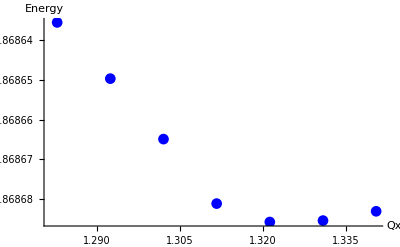

{{1.28282,-0.868636},{1.29242,-0.86865},{1.30202,-0.868665},{1.31161,-0.868681},{1.32121,-0.868686},{1.33081,-0.868685},{1.34041,-0.868683}}

```mathematica
(*Extract real parts*)dataK=Re[qxKPairs];
dataP=Re[qxPPairs];

(*Combine y-components,keep x from qxKPairs (or qxPPairs;assuming x-values match)*)
combinedData=MapThread[{#1[[1]],#1[[2]]+#2[[2]]}&,{dataK,dataP}];

(*Plot the result*)
ListPlot[combinedData,AxesLabel->{"Qx","Energy"},PlotStyle->{Blue,PointSize[Medium]},PlotMarkers->Automatic,PlotRange->All]
combinedData
```

```mathematica
{s0,d0}={0.6175674663771106,1.5850439018133249};Q0=1.325;
{s0,d0}={s,d}/.FindRoot[{fSSg[Q0,s,d],fDSg[Q0,s,d]},{s,s0},{d,d0},Method->"Newton",AccuracyGoal->4,PrecisionGoal->4]
IntKineticIntegrated[Q0,s0,d0]+IntPotentialIntegrated[Q0,s0,d0]
```

{0.618074,1.58553}

```mathematica
-0.8686708053749701-4.50188671377408*^-17 ⅈ+0.8686854544257091
```

0.0000146491-4.50189×10^-17 ⅈ

```mathematica
{Q0,s0,d0}
```

{1.31,0.595038,1.56037}